# Colin’s NYT Crossword Stats

First we set two constants: dataUrl, where the CSV lives (a file in our GitHub repo), and trendWindow, the width of the rolling-median window we’ll smooth the trend with. Note: 90 days is roughly a quarter.

```mathematica
dataUrl="https://raw.githubusercontent.com/colinhb/snippets/refs/heads/main/xword-stats/data.csv";
trendWindow=Quantity[90,"Days"];
```

Next we fix the weekday ordering, Monday through Sunday, and sample seven colors from SolarColors keyed to those days. Defining this once keeps the colors and legend consistent across every chart.

```mathematica
dayOrder={"Monday","Tuesday","Wednesday","Thursday","Friday","Saturday","Sunday"};
dayColors=AssociationThread[dayOrder->(ColorData["SolarColors"]/@Subdivide[6])];
```

Now we pull the CSV down and tidy it. SemanticImport infers each column’s type and parses the ISO date strings into DateObjects for us. We keep only the puzzles that were actually solved and have a recorded time, rename the handful of fields we care about, convert seconds to minutes, and sort by date.

```mathematica
raw=SemanticImport[dataUrl]; 
solved=SortBy[#date&]@Normal@raw[
Select[MatchQ[#"solved",True|"True"]&&NumberQ[#"solving_seconds"]&],
<|"date"->DateObject[#"print_date"],"dayName"->#"day_of_week_name","minutes"->#"solving_seconds"/60.|>
&];
```

Now we use Tukey fences to remove outliers, computed separately for each weekday: anything below Q1 - 1.5 * IQR or above Q3 + 1.5 * IQR is dropped. Doing it per weekday matters because a slow Monday and a fast Saturday sit on completely different scales. More here: Wikipedia.

```mathematica
keepTukey[rows_]:=Module[
{m=#minutes&/@rows,q1,q3,iqr},
{q1,q3}=Quantile[m,{1/4,3/4}];
iqr=q3-q1;
Select[rows,q1-1.5 iqr<=#minutes<=q3+1.5 iqr&]
];
clean=Catenate[keepTukey/@Values@GroupBy[solved,#dayName&]];
```

With the data cleaned, we bucket the rows into one list per weekday, in our Monday-to-Sunday order. This is a more convenient format to iterate over for charting.

```mathematica
byDay=Lookup[GroupBy[clean,#dayName&],dayOrder,{}];
```

Here we assemble the trend chart. scatter is the raw points per day; trend turns each weekday into a TimeSeries and runs a 90-day rolling median over it with MovingMap. We then overlay the faint dots and the median lines, color them by weekday, anchor the y-axis at zero, and attach a legend.

```mathematica
scatter=Map[
Function[rows,{#date,#minutes}&/@rows],
byDay
];
trend=Map[
Function[rows,MovingMap[Median,TimeSeries[{#date,#minutes}&/@rows],trendWindow]],
byDay
];
trendChart=Legended[
Show[
DateListPlot[
scatter,
Joined->False,
PlotStyle->(Directive[#,Opacity[0.35],AbsolutePointSize[2.5]]&/@Values[dayColors])
],
DateListPlot[
trend,
Joined->True,
PlotStyle->(Directive[#,AbsoluteThickness[1.8]]&/@Values[dayColors])
],
PlotRange->{Automatic,{0,Automatic}},(*y-baseline at 0,like zero:true*)
GridLines->Automatic,
Frame->True,
FrameLabel->{"Date","Solve time (minutes)"},
ImageSize->760,
AspectRatio->1/1.7
],
SwatchLegend[Values[dayColors],dayOrder]
];
```

Finally we render it. (Column wraps a single chart for now; it’s where we’d stack additional views in.)

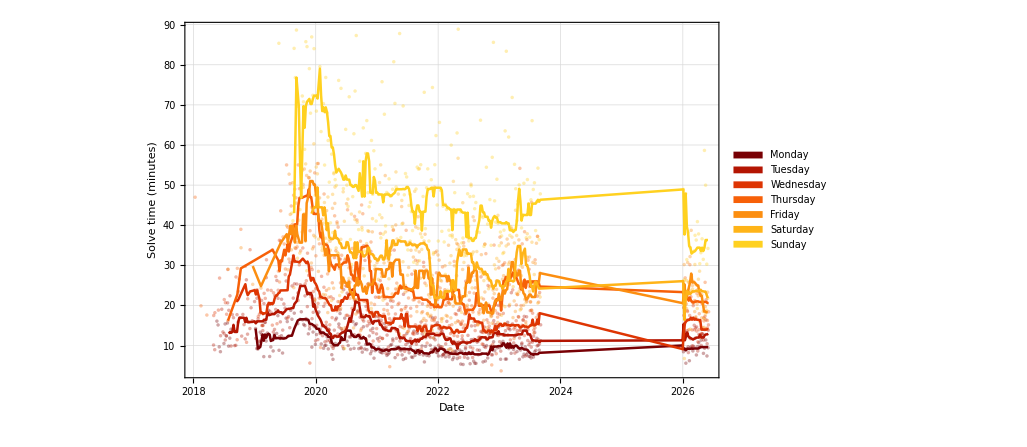

```mathematica
Column[{trendChart}]
```